```mathematica
(* Burgers Vortex Sheet Solution of the Navier-Stokes Equation *)
```

```mathematica
V[x_,y_,z_] = {vx +a x , b y + vy + s S[z], -(a+b)z}; (* velocity field *)
P[x_,y_,z_] =  -(vx+a x)^2/2 - (vy+s+b y)^2/4 - (vy-s+b y)^2/4- (-(a+b)z)^2  /2  ; (* pressure *)
(* Laplace operator *)
Lap[G_, R_] := D[G,{R[[1]],2}]+D[G,{R[[2]],2}] + D[G,{R[[3]],2}]; 
(* Navier-Stokes Equation *)
NSEq[VV_,PP_, R_] := Nu Lap[VV,R] - Grad[VV,R].VV -Grad[PP,R];
```

```mathematica
(* Incompressibility equation *)
```

```mathematica
Div[V[x,y,z],{x,y,z}]
```

0

```mathematica
Seq =S''[z] -> q/Nu z S'[z] + p/Nu S[z]
```

S''[z]→(p S[z])/Nu+(q z S'[z])/Nu

```mathematica
FullSimplify[NSEq[V[x,y,z],P[x,y,z], {x,y,z}]/.Seq]
```

{0,s ((-b+p) S[z]+(a+b+q) z S'[z]),0}

```mathematica
Sol = {p->b,q-> -(a+b)}
```

{p→b,q→-a-b}

```mathematica
FullSimplify[NSEq[V[x,y,z],P[x,y,z], {x,y,z}]/.Seq/.Sol]
```

{0,0,0}

```mathematica
Seqsol = Seq/.Sol
```

S''[z]→(b S[z])/Nu+((-a-b) z S'[z])/Nu

```mathematica
DSolve[S''[z]== p S[z] + q z S'[z],S[z],z][[1]]
```

{S[z]→C[1] HermiteH[-p/q,(√q z)/(√2)]+C[2] Hypergeometric1F1[p/(2 q),1/2,(q z^2)/2]}

```mathematica
absol =Solve[{(-a-2 b)/(a+b)==n, a+ b == c},{a,b}][[1]]
```

{a→2 c+c n,b→-c-c n}

```mathematica
Simplify[V[x,y,z] /.absol/.c->1]
```

{vx+(2+n) x,vy-(1+n) y+s S[z],-z}

```mathematica
SS[n_,z_] := Evaluate[FullSimplify[ⅇ^(-((a+b) z^2)/(2 Nu))  HermiteH[(-a-2 b)/(a+b),(√(a+b) z)/(√2 √Nu)]/.absol/.{c->1,Nu->1}]]
```

```mathematica
SS[n,z]
```

ⅇ^(-z^2/2) HermiteH[n,z/(√2)]

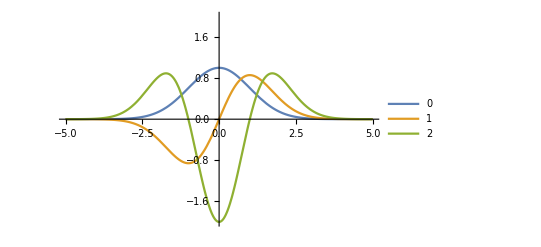

```mathematica
Show[Plot[{SS[0,z],SS[1,z],SS[2,z]},{z,-5,5}, PlotRange->{-2,2},PlotLegends->{0,1,2}]]
```

```mathematica
FullSimplify[FunctionExpand[SS[-1,z] ]]
```

1/2 √π Erfc[z/(√2)]

```mathematica
FullSimplify[FunctionExpand[SS[-2,z] ]]
```

1/4 (2 ⅇ^(-z^2/2)-√(2 π) z Erfc[z/(√2)])

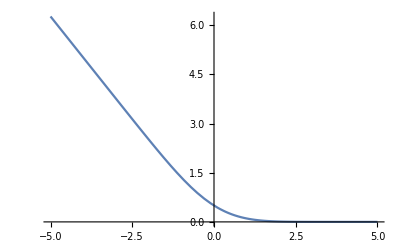

```mathematica
Plot[1/4 (2 ⅇ^(-z^2/2)-√(2 π) z Erfc[z/(√2)]),{z,-5,5}]
```

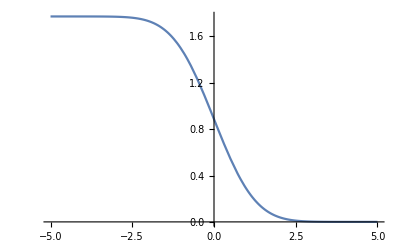

```mathematica
Plot[1/2 √π Erfc[z/(√2)],{z,-5,5}]
```

```mathematica
SS2[n_,z_] := Evaluate[FullSimplify[ⅇ^(-((a+b) z^2)/(2 Nu)) Hypergeometric1F1[-(-a-2 b)/(2 (a+b)),1/2,((a+b) z^2)/(2 Nu)]/.absol/.{c->1,Nu->1}]]
```

```mathematica
SS2[n,z]
```

Hypergeometric1F1[(1+n)/2,1/2,-z^2/2]

```mathematica
FunctionExpand[SS2[0,z]]
```

ⅇ^(-z^2/2)

```mathematica
FullSimplify[FunctionExpand[SS2[1,z]]]
```

1-√2 z DawsonF[z/(√2)]

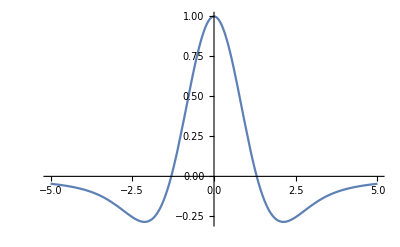

```mathematica
Plot[1-√2 z DawsonF[z/(√2)],{z,-5,5}]
```

```mathematica
Plot[ Erf[z/(√2)],{z,-5,5}]
```